```mathematica
D[Log[Zeta[s]],s]
```

Zeta'[s]/Zeta[s]

```mathematica
Integrate[ Zeta'[s]/Zeta[s],{s,0,Infinity}]
```

-ⅈ π+Log[2]

```mathematica
Log[Zeta[0]]
```

ⅈ π-Log[2]

```mathematica
N[Integrate[ Zeta'[s]/Zeta[s],{s,-I,I}]]
```

0.-3.12581 ⅈ

```mathematica
N[Log[Zeta[I]]-Log[Zeta[-I]]]
```

0.-3.12581 ⅈ

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
dzeta[j_,s_,z_]:=j^-s Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[j]}]
zeta[n_,s_,z_]:=Sum[dzeta[j,s,z],{j,1,n}]
```

```mathematica
FullSimplify[Sum[ dzeta[j,s,-1] D[ zeta[10/j,s,1],s],{j,1,10}]]
```

```mathematica
-Integrate[2520^-s (-315^s (1+2^s+4^s) Log[2]-8^s (35^s (1+3^s) Log[3]+63^s Log[5]+45^s Log[7])),{s,0,Infinity}]
```

16/3

```mathematica
Expand[D[(1-2^(1-s))Zeta[s],s]/((1-2^(1-s))Zeta[s])]/.s->0
```

-2 Log[2]+Log[2 π]

```mathematica
Log[ (1-2^(1-s))Zeta[s]]
```

Log[(1-2^(1-s)) Zeta[s]]

```mathematica
Log[1-2^(1-s)]+Log[Zeta[s]]/.s->0
```

2 ⅈ π-Log[2]

```mathematica
Log[1-2^(1-s)]+Log[Zeta[s]]
```

Log[1-2^(1-s)]+Log[Zeta[s]]

```mathematica
FullSimplify[D[(1-2^(1-s))Zeta[s],s]/((1-2^(1-s))Zeta[s])]
```

Log[4]/(-2+2^s)+Zeta'[s]/Zeta[s]

```mathematica
FullSimplify[D[Log[1-2^(1-s)]+Log[Zeta[s]],s]]
```

Log[4]/(-2+2^s)+Zeta'[s]/Zeta[s]

```mathematica
Log[4]/(-2+2^s)/.s->2
```

Log[4]/2

```mathematica
D[LogIntegral[n^(1-s)]-Log[Log[n^(1-s)]] - EulerGamma,s]
```

Log[n]/Log[n^(1-s)]-(n^(1-s) Log[n])/Log[n^(1-s)]

```mathematica
FullSimplify[Log[n]/Log[1/n]-Log[n]/(n Log[1/n])]
```

```mathematica
Limit[((-1+n) Log[n])/(n Log[1/n]),n->Infinity]
```

-1

```mathematica
N[Log[4]/2]
```

0.693147

```mathematica
D[f[j] j^-s,s]
```

-j^-s f[j] Log[j]

```mathematica
D[f[j]f[k] (j k)^-s,s]
```

-(j k)^-s f[j] f[k] Log[j k]

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
tz[ n_, s_,z_] := Sum[ bin[ z,k] ((1-2^(1-s))Zeta[s]-1)^k,{k,0,n}]
zeros[n_,s_]:=List@@Roots[tz[n,s,z]==0,z][[All,2]]
```

```mathematica
Expand[tz[10,ZetaZero[1],z]]
```

1-(7381 z)/2520+(177133 z^2)/50400-(84095 z^3)/36288+(341693 z^4)/362880-(8591 z^5)/34560+(7513 z^6)/172800-(121 z^7)/24192+(11 z^8)/30240-(11 z^9)/725760+z^10/3628800

```mathematica
N[zeros[30,-5]]
```

{21.3331,21.928,23.0053,23.9996,25.,26.,27.,28.,29.,30.,-2.27531-7.41594 ⅈ,-2.27531+7.41594 ⅈ,2.33424-7.70546 ⅈ,2.33424+7.70546 ⅈ,5.76559-7.33338 ⅈ,5.76559+7.33338 ⅈ,8.61325-6.6668 ⅈ,8.61325+6.6668 ⅈ,11.0822-5.84299 ⅈ,11.0822+5.84299 ⅈ,13.2721-4.92967 ⅈ,13.2721+4.92967 ⅈ,15.241-3.96622 ⅈ,15.241+3.96622 ⅈ,17.0268-2.97847 ⅈ,17.0268+2.97847 ⅈ,18.6566-1.98505 ⅈ,18.6566+1.98505 ⅈ,20.1506-1.001 ⅈ,20.1506+1.001 ⅈ}

```mathematica
Product[ 1-1/j,{j,zeros[30,N[ZetaZero[1]]]}]
```

-1.16733×10^-14

```mathematica
N[(1-2^(1-s))Zeta[s]/.s->2]
```

0.822467

```mathematica
zeros[30,-2.01]
```

{0.939965,1.99652,2.99989,4.,5.,6.00021,6.99928,8.06403,8.43623,9.27978,9.42386,11.0145,11.1107,11.7585,13.2187,13.5727,15.6937,16.1859,18.425,19.0522,22.036,22.2628,24.7523,25.8874,27.0282,28.6258,29.2042,30.9752,31.5193,32.4819}

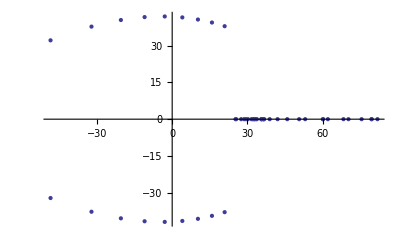

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,zeros[50,.5]}]]
```

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
dzeta[j_,s_,z_]:=j^-s Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[j]}]
zeta[n_,s_,z_]:=Sum[dzeta[j,s,z],{j,1,n}]
p[j_, s_, k_] := D[ dzeta[j,s,z],{z,k}]/.z->0
pz[j_, s_, z_] := Sum[ bin[ z,k] p[j,s,k],{k,1,Log[2,j]}]
```

```mathematica
pz[32,0,z]
```

z/5+5/12 (-1+z) z+7/24 (-2+z) (-1+z) z+1/12 (-3+z) (-2+z) (-1+z) z+1/120 (-4+z) (-3+z) (-2+z) (-1+z) z

```mathematica
pz[16,0,z]
```

z/4+11/24 (-1+z) z+1/4 (-2+z) (-1+z) z+1/24 (-3+z) (-2+z) (-1+z) z

```mathematica
pz[8,0,z]
```

z/3+1/2 (-1+z) z+1/6 (-2+z) (-1+z) z

```mathematica
Expand[pz[36,0,z]]
```

-(3 z)/4+(3 z^2)/2-z^3+z^4/4

```mathematica
pz[2,0,z]
```

z

```mathematica
Table[pz[n,0,z],{n,1,10}]//TableForm
```

0
z
z
z/2+1/2 (-1+z) z
z
(-1+z) z
z
z/3+1/2 (-1+z) z+1/6 (-2+z) (-1+z) z
z/2+1/2 (-1+z) z
(-1+z) z

```mathematica
Clear[rr,zp,zeta, pa, dz, dzalt, Da, zp2]
rr[n_, s_] := rr[n,s] = If[ n==1,0,FullSimplify[ MangoldtLambda[n]/Log[n]] n^-s]
zp[n_,s_,z_,k_]:=zp[n,s,z,k]=Expand[1+z/k Sum[ If[rr[j,s]==0,0,rr[j,s] zp[Floor[n/j],s,z,k+1]],{j,2,n}]]
zp2[n_,s_,z_,k_]:=zp2[n,s,z,k]=Expand[1+z/k Sum[t^-1 Prime[j]^(-s t) zp2[Floor[n/(Prime[j]^t)],s,z,k+1],{t,1,Log[2,n]},{j,1,PrimePi[n^(1/t)]}]]
zeta[n_,s_,z_,k_]:=zeta[n,s,z,,k]=Expand[1+((z+1)/k-1)Sum[j^-s zeta[Floor[n/j],s,z,k+1],{j,2,n}]]
pa[n_,0,a_]:=UnitStep[n-1]
rie[n_] :=rie[n]= Sum[ PrimePi[ n^(1/k)]/k,{k,1,Log[2,n]}]
pa[n_, 1, a_] := pa[n,1,a] = rie[n]-rie[a]
pa[n_,k_,a_]:=pa[n,k,a]=Sum[If[rr[m,0]==0,0,Sum[Binomial[k,j] (rr[m,0])^j pa[Floor[n/(m^j)],k-j,m],{j,1,k}]],{m,a+1,Floor[n^(1/k)]}]
dz[n_, z_] := Sum[ z^k/(k!) pa[n,k,1],{k,0,Log[2,n]}]
Da[n_,k_,a_]:=Da[n,k,a]=Sum[Binomial[k,j] Da[Floor[n/(m^(k-j))],j,m],{m,a+1,n^(1/k)},{j,0,k-1}]
Da[n_,0,a_]:=UnitStep[n-1]
Da[n_,1,a_]:=Floor[n]-a
dzalt[n_,z_]:=Sum[Binomial[z,k] Da[n,k,1],{k,0,Log[2,n]}]
```

```mathematica
Timing[zp[100000,0,z,1]]
```

{7.301,1+(991892879 z)/102960+(16611877533197 z^2)/605404800+(27613425421567 z^3)/864864000+(8883298064606291 z^4)/435891456000+(82938597121 z^5)/10264320+(12123475378339 z^6)/5748019200+(987114594581 z^7)/2612736000+(6832898553167 z^8)/146313216000+(53237749 z^9)/13063680+(1772592397 z^10)/7315660800+(20466961 z^11)/2052864000+(30323737 z^12)/114960384000+(841 z^13)/186810624+(9773 z^14)/209227898880+(71 z^15)/373621248000+(17 z^16)/20922789888000}

```mathematica
Timing[zeta[10000,0,z,1]]
```

{75.208,1+(56175529 z)/45045+(5304616687 z^2)/1663200+(64238883431 z^3)/19958400+(3688608229 z^4)/2177280+(11603252491 z^5)/21772800+(4483862353 z^6)/43545600+(557009347 z^7)/43545600+(2872319 z^8)/2903040+(688397 z^9)/14515200+(58651 z^10)/43545600+(8339 z^11)/479001600+(17 z^12)/95800320+z^13/6227020800}

```mathematica
Timing[dz[100000000,z]]
```

{0.,1+(6427431691337929 z)/1115464350+(2516314672020796036867 z^2)/128629994613120+(3575746713648621345062531 z^3)/124672148625024000+(20380394053499739865496567 z^4)/831147657500160000+(1351629191016384695492785649 z^5)/97569507619584000000+(240272276318313590611783219 z^6)/43364225608704000000+(41833655627451907360857929 z^7)/25545471085854720000+(3761102376291956378646751 z^8)/10218188434341888000+(5175675474335907053437241 z^9)/80669908692172800000+(1418826547912276016443177 z^10)/161339817384345600000+(279266312199608569103 z^11)/292017769021440000+(1386818791325659005283 z^12)/16703416388026368000+(4814640871442135348159 z^13)/835170819401318400000+(3482068013538497942357 z^14)/10857220652217139200000+(1188915869941720073 z^15)/83517081940131840000+(4192807585604237 z^16)/8351708194013184000+(17963977627832867 z^17)/1290718539074764800000+(390742194213977 z^18)/1290718539074764800000+(1555110247813 z^19)/306545653030256640000+(31437955243 z^20)/490473044848410624000+(14797988921 z^21)/24523652242420531200000+(976022221 z^22)/269760174666625843200000+(786869 z^23)/47726800133326110720000+(1493 z^24)/38778025108327464960000+(727 z^25)/31022420086661971968000000+z^26/403291461126605635584000000}

```mathematica
Timing[dzalt[10000000,4]]
```

{10.764,8840109380}

```mathematica
Timing[zp2[10000000,0,z,1]]
```

{206.686,1+(3559637526370229 z)/5354228880+(1989544871269240547 z^2)/921858537600+(2021824016451264335171 z^3)/677566025136000+(7019677821920298561119 z^4)/2956651746048000+(6419737164240558941381 z^5)/5217620728320000+(355971199127948600783 z^6)/800296713216000+(87671088330394680791 z^7)/750278168640000+(647852562694427393 z^8)/28245766348800+(1156246192125011873 z^9)/337983528960000+(6208422327896021939 z^10)/15817629155328000+(250225399924000051 z^11)/7189831434240000+(6106970322634813 z^12)/2549361475584000+(63437608022863169 z^13)/497125487738880000+(47189432328823 z^14)/9038645231616000+(17111105280953 z^15)/105450861035520000+(120162307939 z^16)/31635258310656000+(179878582253 z^17)/2688996956405760000+(2349779 z^18)/2845499424768000+(53393233 z^19)/7298706024529920000+(94223 z^20)/2919482409811968000+(13 z^21)/154120489205760000+(53 z^22)/224800145555521536000+z^23/25852016738884976640000}

```mathematica
Timing[zp2[100000,N[ZetaZero[1]],z,1]]
```

{4.197,1-(4.33543-1.75998 ⅈ) z+(1.19578+4.25396 ⅈ) z^2-(7.46539-6.53483 ⅈ) z^3-(0.917224-3.46318 ⅈ) z^4-(1.74755-1.97308 ⅈ) z^5-(0.176183-0.396989 ⅈ) z^6-(0.0860726-0.118227 ⅈ) z^7-(0.00552684-0.00965199 ⅈ) z^8-(0.000985228-0.00177868 ⅈ) z^9-(0.0000455564-0.0000486405 ⅈ) z^10-(2.29571×10^-6-6.4587×10^-6 ⅈ) z^11-(1.31806×10^-7-4.38354×10^-8 ⅈ) z^12+(6.2637×10^-10+4.16854×10^-9 ⅈ) z^13-(6.24985×10^-11-4.10989×10^-11 ⅈ) z^14+(1.94312×10^-13-1.48812×10^-13 ⅈ) z^15+(1.74515×10^-15+1.92705×10^-15 ⅈ) z^16}

```mathematica
Timing[PrimePi[10^13]]
```

{0.,346065536839}

```mathematica
10^8
```

100000000

```mathematica
CountPrimes[1000]
```

168

```mathematica
WheelEntries=5;
WheelSize:=Product[Prime[j],{j,1,WheelEntries}];
CoprimeCache:=Table[CoprimeQ[WheelSize,n],{n,1,WheelSize}]
Use[n_]:=If[CoprimeCache[[Mod[n-1,WheelSize]+1]]==True,1,0]
LegendrePhi[x_,a_]:=LegendrePhi[x,a-1]-LegendrePhi[x/Prime[a],a-1]
LegendrePhi[x_,0]:=Floor[x]
LegPhiCache:=LegPhiCache=Table[LegendrePhi[n,WheelEntries],{n,1,WheelSize}]
FullWheel:=LegendrePhi[WheelSize,WheelEntries];
Coprimes[n_]:=LegPhiCache[[Mod[n-1,WheelSize]+1]]+Floor[(n-1)/WheelSize]FullWheel
d[n_,0,a_]:=1
d[n_,1,a_]:=Coprimes[n]-Coprimes[a]
d[n_,k_,a_]:=Sum[If[ Use[m]==0,0,Binomial[k,j] d[Floor[n/(m^(k-j))],j,m]],{m,a+1,n^(1/k)},{j,0,k-1}]
RiemannPrimeCounting[n_]:=Sum[(-1)^(k+1)/k  d[Floor[n],k,1],{k,1,Log[2,n]}]
CountPrimes[ n_] := WheelEntries+Sum[MoebiusMu[k] RiemannPrimeCounting[n^(1/k)]/k,{k,1,Log[2,n]}]
```

```mathematica
CountPrimes[10000000]
```

664579

```mathematica
d[n_,0,a_]:=1
d[n_,1,a_]:=Floor[n]-a
d[n_,k_,a_]:=Sum[Binomial[k,j] d[Floor[n/(m^(k-j))],j,m],{m,a+1,n^(1/k)},{j,0,k-1}]
RiemannPrimeCounting[n_]:=Sum[(-1)^(k+1)/k  d[n,k,1],{k,1,Log[2,n]}]
CountPrimes[ n_] := Sum[MoebiusMu[k] RiemannPrimeCounting[n^(1/k)]/k,{k,1,Log[2,n]}]
```

```mathematica
Timing[CountPrimes[10000000]]
```

{32.573,664579}

```mathematica
Timing[PrimePi[10^13]]
```

{12.293,346065536839}

```mathematica
Limit[ (1+y^(s-1) HurwitzZeta[ s,1+y])^z,y->Infinity]
```

(s/(-1+s))^z

```mathematica
10^7
```

10000000